```mathematica
a=1;b=2;ρ=(a+b)/2
```

3/2

```mathematica
U[ρ_,φ_,nMax_]:=∑_(n=0)^nMax An[n]*(-b^(4n+1)*ρ^(-1-2n)+ρ^(2n))*LegendreP[2*n,Cos[φ]]
```

```mathematica
An[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^π T*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
```

```mathematica
1.(*Trial*)
```

```mathematica
Utrial[ρ_,φ_]:=-36(-b*ρ^-1+ρ^0)
```

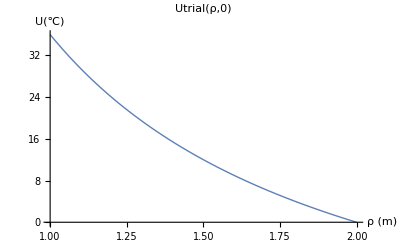

```mathematica
Plot[Utrial[ρ,0],{ρ,a,b},PlotLabel->"Utrial(ρ,0)", PlotRange->All,AxesLabel->{"ρ (m)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

```mathematica
(*Critical point:*)
```

```mathematica
Utrial[(a+b)/2,0]
```

12

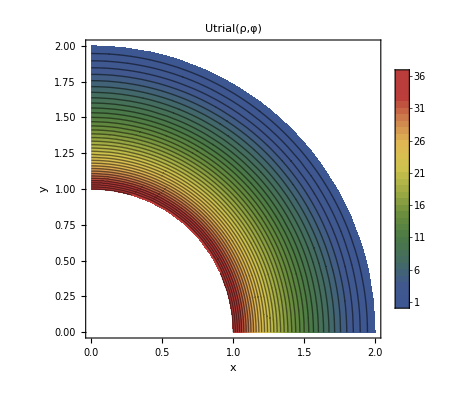

```mathematica
ContourPlot[Utrial[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],PlotLabel->"Utrial(ρ,φ)",BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,100,1],PlotLegends->Automatic]
```

```mathematica
2.(*Final*)
```

```mathematica
Solve[ A0*(ρ^0-b^1*ρ^-1)+A1*LegendreP[2,Cos[0]]*(-b^5*ρ^-3+ρ^2)==12&& A0*(ρ^0-b^1*ρ^-1)+A1*LegendreP[2,Cos[π/4]]*(-b^5*ρ^-3+ρ^2)==6,{A0,A1}]
```

{{A0→-12,A1→-864/781}}

```mathematica
Anfinal[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^(π/2) (c*(Cos[φ])^2+d)*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
```

```mathematica
Anfinal[0]
```

-c/3-d

```mathematica
Anfinal[1]
```

-(2 c)/93

```mathematica
Solve[ -c/3-d==-12&&-(2 c)/93==-864/781,{c,d}]
```

{{c→40176/781,d→-4020/781}}

```mathematica
Tfinal[φ_]:=40176/781*(Cos[φ])^2-4020/781
```

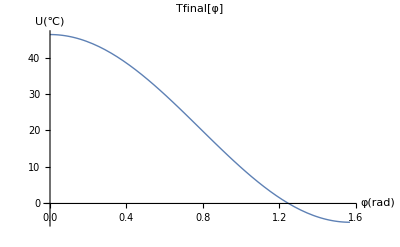

```mathematica
Plot[Tfinal[φ],{φ,0,π/2},PlotLabel->"Tfinal[φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

```mathematica
ufinal[ρ_,φ_]:=-12*(ρ^0-b^1*ρ^-1)-864/781*LegendreP[2,Cos[φ]]*(-b^5*ρ^-3+ρ^2)
```

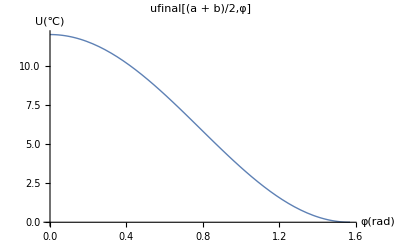

```mathematica
Plot[ufinal[(a+b)/2,φ],{φ,0,π/2},PlotLabel->"ufinal[(a + b)/2,φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

```mathematica
(*Critical point:*)
ufinal[(a+b)/2,0]
ufinal[(a+b)/2,π/4]
```

12

6

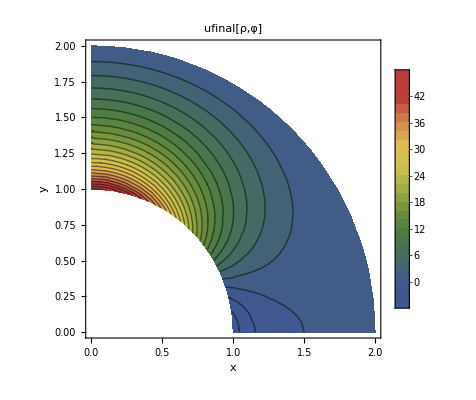

```mathematica
ContourPlot[ufinal[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],PlotLabel->"ufinal[ρ,φ]",BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,100,2],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
3.(*extension*)
```

```mathematica
Solve[B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[0]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[0]]*(-b^17*ρ^-9+ρ^8)==12&&B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[π/4]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[π/4]]*(-b^17*ρ^-9+ρ^8)==6&&B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[π/8]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[π/8]]*(-b^17*ρ^-9+ρ^8)==9,{B0,B1,B2}]
```

{{B0→-(6 (19-42 Cos[π/8]^2+20 Cos[π/8]^4))/(5 (1-3 Cos[π/8]^2+2 Cos[π/8]^4)),B1→-(216 (1-48 Cos[π/8]^2+56 Cos[π/8]^4))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4)),B2→(241864704 (-3+4 Cos[π/8]^2))/(596775515735 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))}}

```mathematica
uextension[ρ_,φ_]:=-(6 (19-42 Cos[π/8]^2+20 Cos[π/8]^4))/(5 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))*(ρ^0-b^1*ρ^-1)-(216 (1-48 Cos[π/8]^2+56 Cos[π/8]^4))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))*LegendreP[2,Cos[φ]]*(-b^5*ρ^-3+ρ^2)+(241864704 (-3+4 Cos[π/8]^2))/(596775515735 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))(-b^17*ρ^-9+ρ^8)*LegendreP[4,Cos[φ]]
```

```mathematica
Anextension[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^(π/2) (uextension[a,φ])*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
```

```mathematica
Anextension[0]
Anextension[1]
Anextension[2]
Anextension[3]
```

-132/5

1728/5467

-126805794471936/304952288540585

0

```mathematica
Ann[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^(π/2) (p*(Cos[φ])^4+q*(Cos[φ])^2+s)*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
Ann[0]
Ann[1]
Ann[2]
Ann[3]
```

-p/5-q/3-s

-2/651 (6 p+7 q)

-(8 p)/17885

0

```mathematica
Solve[-p/5-q/3-s==-132/5&&-2/651 (6 p+7 q)==1728/5467&&-(8 p)/17885==-126805794471936/304952288540585,{p,q,s}]
```

{{p→15850724308992/17050729021,q→-10806650612890272/13316619365401,s→1477892485145460/13316619365401}}

```mathematica
Textension[φ_]:=15850724308992/17050729021*(Cos[φ])^4+-10806650612890272/13316619365401*(Cos[φ])^2+1477892485145460/13316619365401
```

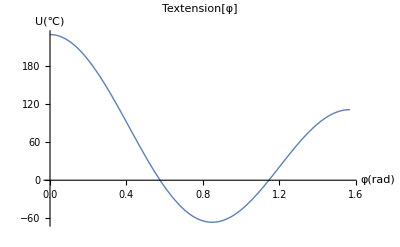

```mathematica
Plot[Textension[φ],{φ,0,π/2},PlotLabel->"Textension[φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

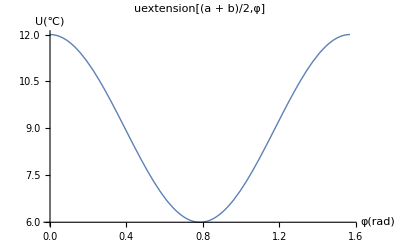

```mathematica
Plot[uextension[(a+b)/2,φ],{φ,0,π/2},PlotLabel->"uextension[(a + b)/2,φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

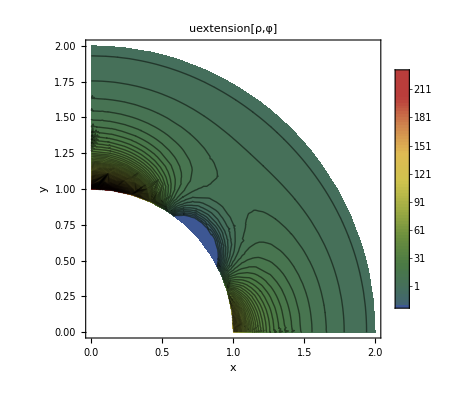

```mathematica
ContourPlot[uextension[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],PlotLabel->"uextension[ρ,φ]",BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,560,3],PlotRange->All,PlotLegends->Automatic]
```